```mathematica
Clear["Global`*"]
```

```mathematica
J=22;
hplus=-5;
hminus=-15;
NSolve[m==1/4(1+Tanh[(hplus+J m)/2])+1/4(1+Tanh[(hminus+J m)/2]),m,Reals]
```

{{m→0.00362216},{m→0.214133},{m→0.510222},{m→0.638017},{m→0.99954}}

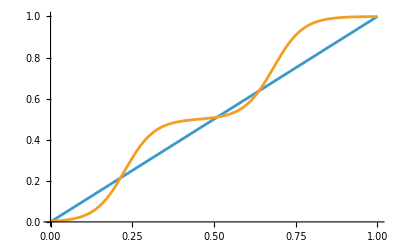

```mathematica
Plot[{m,1/4(1+Tanh[1/2(hplus+J m)])+1/4(1+Tanh[1/2(hminus+J m)])},{m,0,1}]
```

```mathematica
(*Define constants*)
J=22; (*Fixed coupling constant-adjust this value as needed*)
hdelta=5;

(*Define the equation as a function*)
eqn[hmean_,hdelta_,m_]:=m-(1/4 (1+Tanh[1/2(hmean+hdelta+J m)])+1/4 (1+Tanh[1/2(hmean-hdelta+J m)]));

(*Function to find all real solutions for given n and hplus*)
findSolutions[hmean_]:=Module[{sols,validSols},sols=NSolve[eqn[hmean,hdelta,m]==0&&0<=m<=1,m,Reals];
validSols=m/. sols;
(*Pad with NaN if fewer than expected solutions*)
PadRight[validSols,5,Undefined]]
```

```mathematica
(*Define parameter ranges*)
hmeanRange={-15,-5};

(*Create a grid of parameter values*)
hmeanVals=Range[hmeanRange[[1]],hmeanRange[[2]],0.05];

(*Calculate solutions for all parameter combinations*)
solutionData=Table[{hmean,findSolutions[hmean]},{hmean,hmeanVals}];

(*Extract individual solution surfaces*)
extractSurface[solutionIndex_]:=Table[With[{sols=solutionData[[i,2]]},If[Length[sols]>=solutionIndex&&NumericQ[sols[[solutionIndex]]],{solutionData[[i,1]],sols[[solutionIndex]]},Nothing]],{i,Length[hmeanVals]}];

(*Get data for up to 3 solution branches*)
surface1=extractSurface[1];
surface2=extractSurface[2];
surface3=extractSurface[3];
surface4=extractSurface[4];
surface5=extractSurface[5];
```

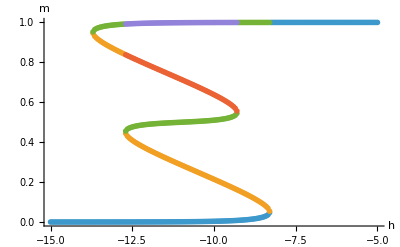

```mathematica
ListPlot[{surface1,surface2,surface3,surface4,surface5},AxesLabel->{"h","m"},PlotStyle->PointSize[.01]]
```

```mathematica
(*Define the equation as a function*)
susceptibility[hmean_,hdelta_,m_,mp_]:=mp-1/8(1+J mp) (Sech[1/2(hmean+hdelta+J m)]^2+Sech[1/2(hmean-hdelta+J m)]^2);

(*Function to find all real solutions for given n, hplus, m_*)
findSusceptbility[hmean_,m_]:=Module[{sols,validSols},sols=NSolve[susceptibility[hmean,hdelta,m,mp]==0,mp,Reals];
validSols=mp/. sols]
```

```mathematica
(*Extract individual solution surfaces*)
extractSusSurface[solutionData_]:=Table[With[{sols=solutionData[[i]][[2]]},{solutionData[[i]][[1]],sols[[1]]}],{i,Length[solutionData]}];

(*Calculate solutions for all parameter combinations*)
solutionData=Table[{params[[1]],findSusceptbility[params[[1]],params[[2]]]},{params,surface1}];
susSurface1=extractSusSurface[solutionData];
solutionData=Table[{params[[1]],findSusceptbility[params[[1]],params[[2]]]},{params,surface2}];
susSurface2=extractSusSurface[solutionData];
solutionData=Table[{params[[1]],findSusceptbility[params[[1]],params[[2]]]},{params,surface3}];
susSurface3=extractSusSurface[solutionData];
```

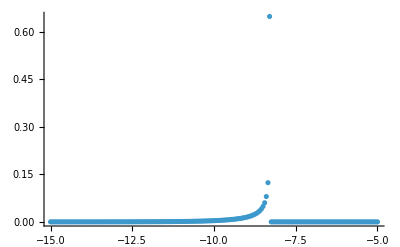

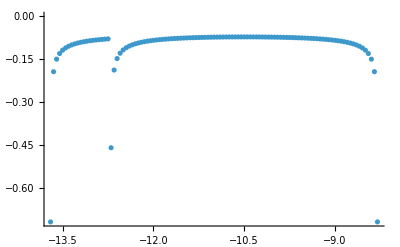

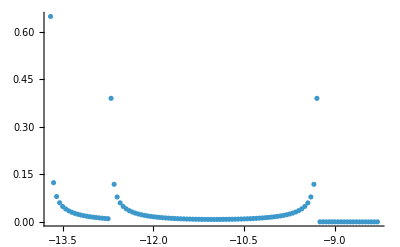

```mathematica
ListPlot[susSurface1,PlotLegends->Automatic,PlotRange->All]
ListPlot[susSurface2,PlotLegends->Automatic,PlotRange->All]
ListPlot[susSurface3,PlotLegends->Automatic,PlotRange->All]
```

#### Additional plotting tools

```mathematica
(*Optional:Interactive manipulation*)
Manipulate[With[{sols=findSolutions[n,hplus]},Column[{Plot[{1/4 (1+Tanh[hplus+2 J (n-1) m])+1/4 (1+Tanh[hminus+2 J (n-1) m]),m},{m,-2,2},PlotStyle->{Blue,Red},PlotLegends->{"RHS","LHS"},PlotLabel->"Graphical solution (J = "<>ToString[J]<>")",Epilog->{PointSize[Large],Black,Point[Table[{sol,sol},{sol,DeleteCases[sols,Undefined]}]]}],"Solutions: "<>ToString[DeleteCases[sols,Undefined]]}]],{n,50,200,5},{hplus,-5,1,0.1},{hminus,-10,-1,0.1}]

(*Additional:Explore different J values*)
Manipulate[Module[{eqnJ,solsJ},eqnJ[n_,hplus_,m_]:=m-(1/4 (1+Tanh[hplus+2 Jval (n-1) m])+1/4 (1+Tanh[hminus+2 Jval (n-1) m]));
solsJ=m/. NSolve[eqnJ[n,hplus,m]==0&&-2<=m<=2,m,Reals];
Plot[{1/4 (1+Tanh[hplus+2 Jval (n-1) m])+1/4 (1+Tanh[hminus+2 Jval (n-1) m]),m},{m,-2,2},PlotStyle->{Blue,Red},PlotLegends->{"RHS","LHS"},PlotLabel->"Effect of J on solutions (J = "<>ToString[Jval]<>")",Epilog->{PointSize[Large],Black,Point[Table[{sol,sol},{sol,solsJ}]]}]],{Jval,0.01,1,0.01},{n,50,200,5},{hplus,-5,1,0.1},{hminus,-10,-1,0.1}]
```